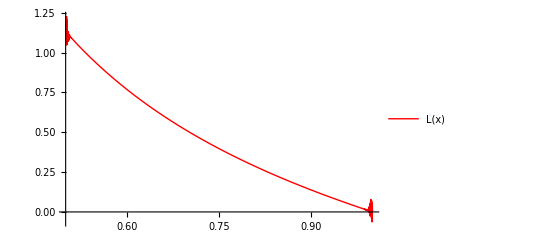

```mathematica
(*Зададим коэффициенты данного дифференциального уравнения*)
p[x_]=-1/x;
q[x_]=-3/x^2;
f[x_]=3/x^2;
(*Зададим краевые условия*)
a=1/2;
alpha0=1;
alpha1=1/2;
A=-1;
b=1;
beta0=1;
beta1=0;
B=0;
(*Зададим количество частичных отрезков*)
n=50;
(*Найдем шаг разбиения*)
h=(b-a)/n;
(*Построим разбиение отрезка на частичные*)
X=Table[a+k*h,{k,0,n}];
(*Построим сеточные функции*)
P=Table[p[X[[k]]],{k,1,n+1}];
Q=Table[q[X[[k]]],{k,1,n+1}];
F=Table[f[X[[k]]],{k,1,n+1}];
(*Зададим основную матрицу системы уравнений для поиска каркаса приближенного решения*)
K=Table[0,{i,1,n+1},{j,1,n+1}];
(*Зададим элементы матрицы, которые получаются после дискретизации данного дифференциального уравнения*)
j=2;
For[i=1,i≤n-1,i++,
K[[i,j-1]]=1/h^2-P[[j]]/(2*h);
K[[i,j]]=Q[[j]]-2/h^2;
K[[i,j+1]]=1/h^2+P[[j]]/(2*h);
j=j+1;
]
(*Добавим элементы матрицы, которые получаются после дискретизации граничных условий*)
(*Добавим первое граничное условие*)
K[[n,1]]=alpha0-alpha1/h;
K[[n,2]]=alpha1/h;
(*Добавим второе граничное условие*)
K[[n+1,n]]=-beta1/h;
K[[n+1,n+1]]=beta0+beta1/h;
(*Построим столбец свободных членов системы уравнений*)
T=Table[F[[i]],{i,2,n}];
AppendTo[T,A];
AppendTo[T,B];
Y=Inverse[K].T;
(*Выполним интерполяцию приближенного решения многочленом Лагранжа*)L[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
GR=Plot[L[x],{x,a,b},PlotStyle->Red,PlotLegends->"Expressions"]
```

(1-x)/x

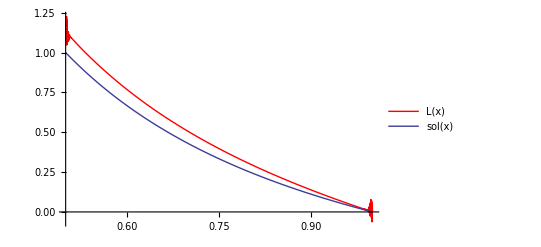

```mathematica
(*Найдем точное решение данной задачи, используя встроенные средства*)
Sol=DSolve[{s''[x]+p[x]*s'[x]+q[x]*s[x]==f[x],alpha0*s[a]+alpha1*s'[a]==A,beta0*s[b]+beta1*s'[b]==B},s[x],x];
sol[x_]=s[x]/.Sol[[1]]
G=Plot[sol[x],{x,a,b},PlotLegends->"Expressions"];
(*Построим графики приближенного и точного решения*)
Show[GR,G]
```